## Constant

```mathematica
ve=232*10^3/(3*10^8);(*1*)
v0=220*10^3/(3*10^8);(*1*)
vesc=544*10^3/(3*10^8);(*1*)
NT=7.89316*10^24;(*The number of NaI per kg,/kg*)
A=22.99;(*1*)
mN=21.4607;(*The mass of Na, unit: GeV*)
ρ=2.2936118999999997*10^-42; (*ρ=0.3GeV/cm^3 in nature unit:GeV^4. 1cm=51000 eV^-1=5.1*10^13/GeV from wikipedia*)
qNa=0.3;
ℏ=6.566666666666667*10^-19;(*keV·s*)
```

## N_smooth

```mathematica
Ns=v0^3 π^(3/2) Erf[vesc/v0]-2 π v0^2 vesc ⅇ^(-vesc^2/v0^2)-4/3 π vesc^3 ⅇ^(-vesc^2/v0^2);
```

## Form Factor Function

```mathematica
F[E_]:=Module[{s,A,a,r,c,q},
s=0.9;A=23;a=0.52;
c=1.23 A^(1/3)-0.6;
r=√(c^2+7/3 π^2 a^2-5 s^2);
q=√(2 mN E);
3 E^(-(q^2 s^2)/(2*(0.197)^2)) (Sin[q r/0.197]-q r Cos[q r/0.197]/0.197)/(q r/0.197)^3];(*unit 1, [q]=GeV, [r]=fm as we use the relation 1=0.197GeV*fm*)
```

## Event Rate Function

```mathematica
EventRate[mχ_,σχp_,ER_]:=Module[{a,b,μ,vmin,c,VA},
μ=(mN mχ)/(mN+mχ);vmin=√((mN (ER*10^-6))/(2 μ^2));(*[mN]=[mχ]=[μ]=[ER*10^-6]=GeV*)
a=vesc/v0;b=ve/v0;c=vmin/v0;
VA=If[vmin>vesc+ve,0,
If[vesc-ve<vmin<vesc+ve,
(π^(3/2) v0^2)/(2 b Ns)(Erf[a]+Erf[b-c]-(2 ⅇ^(-a^2))/(3 √π) (a+b-c) (3+(a+b-c)(2 a-b+c))),
(π^(3/2) v0^2)/(2 b Ns) (Erf[b-c]+Erf[b+c]+(4 b ⅇ^(-a^2))/(√π) (-1-a^2+c^2+b^2/3))]];
(NT mN ρ)/(2 mχ μ^2)σχp F[(ER*10^-6)]^2 VA A^2/ℏ];(*[NT]=kg^-1,[mN]=[mχ]=[μ]=GeV,[ρ]=GeV*)
```

## Test

```mathematica
24*60*60*EventRate[10,2.6*10^-13,2]
```

0.00569175

## Plot

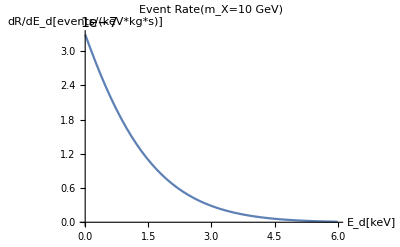

```mathematica
Plot[EventRate[10,2.6*10^-13,x/qNa]/qNa,{x,10^-3,6},
AxesLabel->{"E_d[keV]","dR/dE_d[events/(keV*kg*s)]"},PlotLabel->HoldForm[Event Rate  [Subscript[m, Χ]=10 GeV]],LabelStyle->{GrayLevel[0]}]
```

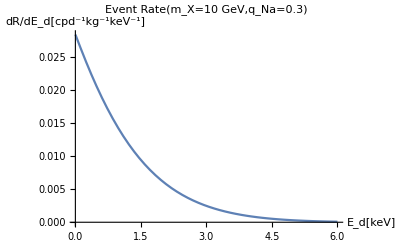

```mathematica
Plot[24*60*60*EventRate[10,2.6*10^-13,x/qNa]/qNa,{x,10^-3,6},
AxesLabel->{"E_d[keV]","dR/dE_d[cpd^-1kg^-1keV^-1]"},PlotLabel->HoldForm[Event Rate  [Subscript[m, Χ]=10 GeV, Subscript[q, Na]=0.3]],LabelStyle->{GrayLevel[0]}]
```

## Annual Modulation Function

```mathematica
AEventRate[mχ_,σχp_,ER_,t_]:=Module[{a,b,μ,vmin,c,VA},
μ=(mN mχ)/(mN+mχ);vmin=√((mN (ER*10^-6))/(2 μ^2));
a=vesc/v0;b=v[t]/v0;c=vmin/v0;
VA=If[vmin>vesc+v[t],0,
If[vesc-v[t]<vmin<vesc+v[t],
(π^(3/2) v0^2)/(2 b Ns)(Erf[a]+Erf[b-c]-(2 ⅇ^(-a^2))/(3 √π) (a+b-c) (3+(a+b-c)(2 a-b+c))),
(π^(3/2) v0^2)/(2 b Ns) (Erf[b-c]+Erf[b+c]+(4 b ⅇ^(-a^2))/(√π) (-1-a^2+c^2+b^2/3))]];
(NT mN ρ)/(2 mχ μ^2)σχp F[(ER*10^-6)]^2 VA A^2/ℏ];

v[t_]:=(232+14 Cos[(2 π)/365.25 (t*365-152)])/(3 10^5);
```

## Lists

```mathematica
L5=Table[10,{365}];
L6=Table[2.576721894405937*10^-13,{365}];
L7=Table[2*10^-6,{365}];
L8=Table[i,{i,1/365,1,1/365}];
```

## Plot

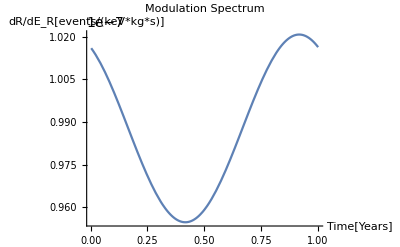

```mathematica
Plot[AEventRate[10,2.6*10^-13,2*10^-6/qNa,x],{x,1/365,1},
AxesLabel->{"Time[Years]","dR/dE_R[events/(keV*kg*s)]"},PlotLabel->HoldForm[Modulation Spectrum],LabelStyle->{GrayLevel[0]}]
```

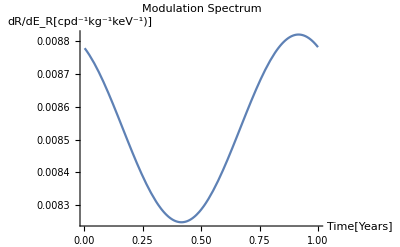

```mathematica
Plot[24*60*60*AEventRate[10,2.6*10^-13,2*10^-6/qNa,x],{x,1/365,1},
AxesLabel->{"Time[Years]","dR/dE_R[cpd^-1kg^-1keV^-1)]"},PlotLabel->HoldForm[Modulation Spectrum],LabelStyle->{GrayLevel[0]}]
```

## Modulation Amplitude

```mathematica
Amplitude=(Max[MapThread[AEventRate,{L5,L6,L7,L8}]]-Min[MapThread[AEventRate,{L5,L6,L7,L8}]])/2
```

3.28195×10^-9

## χ^2

```mathematica
rateex={0.016,0.026,0.022,0.008,0.011,0.005,0.009,0.004};
sigma={0.004,0.005,0.005,0.005,0.004,0.004,0.003,0.003};
χ[th_,ex_,σ_]:=((th-ex)/σ)^2;
χ2[m_,σχ_]:=Module[{rateth},
rateth=24*60*60/0.3*MapThread[EventRate,{Table[m,{8}],Table[σχ,{8}],{2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75}/0.3}];
Apply[Plus,MapThread[χ,{rateth,rateex,sigma}]]];
χ2[10,2.576721894405937*10^-13]
```

64.8667

```mathematica
evector={2.25,2.75,3.25,3.75,4.25,4.75,5.25,5.75}/0.3;
χ2test[m_,σχ_]:=Module[{rateth},
rateth=24*60*60/0.3*EventRate[m,σχ,#]&/@evector;
Apply[Plus,MapThread[χ,{rateth,rateex,sigma}]]];
```

```mathematica
χ2test[10,2.576721894405937*10^-13]
```

64.8667

## Scan χ^2

```mathematica
m=Table[i,{i,5,20,0.1}];
l=Table[k*2.576721894405937*10^-14,{k,1,100,1}];
scan=Outer[χ2,m,l];
```

```mathematica
BMP=Min[scan]
Position[scan,BMP]
```

8.706

(145 | 64)

## RegionPlot

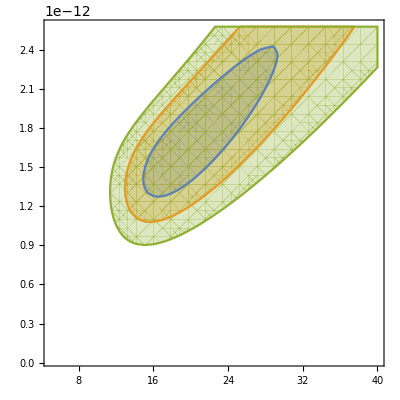

```mathematica
RegionPlot[{χ2[m,l]≤BMP+2.30,χ2[m,l]≤BMP+6.18,χ2[m,l]≤BMP+11.83},{m,5,40},{l,2.576721894405937*10^-14,2.576721894405937*10^-12}]
```

## XENON100

```mathematica
ve=232*10^3/(3*10^8);(*1*)
v0=220*10^3/(3*10^8);(*1*)
vesc=600*10^3/(3*10^8);(*1*)
NT=4.59542*10^24;(*The number of Xe per kg,/kg*)
A=131;(*1*)
mN=122.522;(*The mass of Xe, unit: GeV*)
ρ=0.3; (*ρ=0.3GeV/cm^3 in nature unit:GeV^4. 1cm=51000 eV^-1=5.1*10^13/GeV from wikipedia*)
ℏ=6.566666666666667*10^-19;(*keV*s*)
```

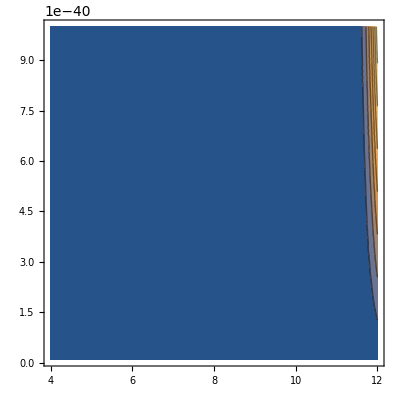

```mathematica
ContourPlot[EventRate[M,σ,4/0.3],{M,4,12},{σ,10^-41,10^-39}]
```